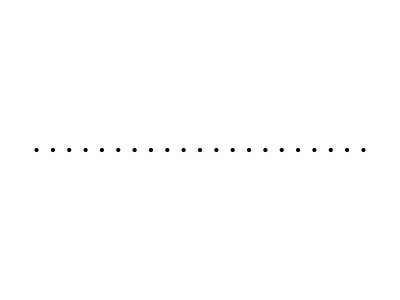

```mathematica
x1=-1;
x2=1;
h1=0.5;
Graphics[{
{PointSize[Large],Point[Table[{i,h1},{i,x1,x2,0.1}]]}
}]
```

```mathematica
Manipulate[
Module[{r,f1,f2,θ1,x1,x2,h1},
r=6.204;
f1[x_]=-√(r^2-x^2)+r;
f2[x_]=√(r^2-x^2)+r;

h1=h*2;

θ1=ArcSin[(r-h1)/r];x1=r*Cos[-π-θ1];x2=r*Cos[θ1];

Show[
Graphics[{
Table[{
PointSize[RandomReal[{0.01,0.045}]],
Point[{RandomReal[{x1,x2}],h1}]
},{20}],
{Blue,Thick,Line[{{-r,hW},{r,hW}}]}
}],
Plot[{f1[x],f2[x]},{x,-r,r},PlotStyle->{{Thick,Black},{Thick,Black}}],AspectRatio->Automatic]
],
{{hW,6.204,"water height"},0.4,8,0.01,Appearance->"Labeled"},
{{h,0.5,""},0.2,1,0.1,Appearance->"Labeled"}]
```

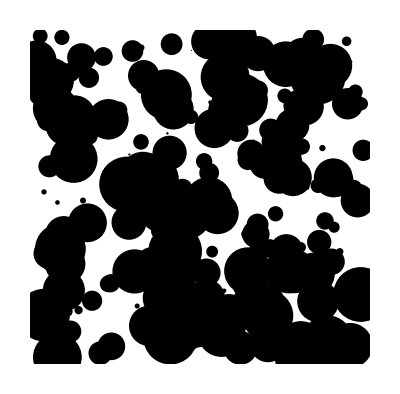

```mathematica
Graphics[
Table[{
PointSize[RandomReal[{0,0.1}]],
Point[{RandomReal[{x1,x2}],h1}]
},{200}]
]
```